```mathematica
Lecture 5: Substutions, Iteration
```

## Substitutions

### Exercise Subsection

What does the following cell do?

```mathematica
Clear[x,y]
```

```mathematica
ReplaceAll[x^2+y^2,{x->1,y->x}]
ReplaceRepeated[x^2+y^2,{x->1,y->x}]
x^2+y^2/.{x->1,y->x}
x^2+y^2//.{x->1,y->x}
```

1+x^2

2

1+x^2

2

### Exercise Subsection

What does the following cell do?

```mathematica
ReplaceAll[x^2+1,#]&/@Solve[(x-1)(x-2)(x-3)==0,x]
```

{2,5,10}

```mathematica
Solve[(x-1)(x-2)(x-3)==0,x]
```

{{x→1},{x→2},{x→3}}

### Exercise Subsection

What do the following cells do when evaluated?

```mathematica
x^2+y^2/.{a_^b_->b^a}
```

2^x+2^y

```mathematica
3 x^2-5x+1/.{a_ x^2+b_ x +c_ -> 2 a x + b}
```

-5+6 x

```mathematica
{{a,b},{c,d},{e,f},{g,i,h}}/.{{x_,y_}->x/y}
```

{a/b,c/d,e/f,{g,i,h}}

### Exercise Subsection

What does the following cell do?

```mathematica
Permutations@Range@3/.{a_,b_,c_}-> x^a  y^b z^c
```

{x y^2 z^3,x y^3 z^2,x^2 y z^3,x^2 y^3 z,x^3 y z^2,x^3 y^2 z}

### Exercise Subsection

Produce the same output as the cell below in a few different ways.

```mathematica
Tuples[Range@5,2]/.{a_,b_}->a+I b
```

{1+ⅈ,1+2 ⅈ,1+3 ⅈ,1+4 ⅈ,1+5 ⅈ,2+ⅈ,2+2 ⅈ,2+3 ⅈ,2+4 ⅈ,2+5 ⅈ,3+ⅈ,3+2 ⅈ,3+3 ⅈ,3+4 ⅈ,3+5 ⅈ,4+ⅈ,4+2 ⅈ,4+3 ⅈ,4+4 ⅈ,4+5 ⅈ,5+ⅈ,5+2 ⅈ,5+3 ⅈ,5+4 ⅈ,5+5 ⅈ}

```mathematica
Flatten@Table[a+I b,{a,1,5},{b,1,5}]
```

{1+ⅈ,1+2 ⅈ,1+3 ⅈ,1+4 ⅈ,1+5 ⅈ,2+ⅈ,2+2 ⅈ,2+3 ⅈ,2+4 ⅈ,2+5 ⅈ,3+ⅈ,3+2 ⅈ,3+3 ⅈ,3+4 ⅈ,3+5 ⅈ,4+ⅈ,4+2 ⅈ,4+3 ⅈ,4+4 ⅈ,4+5 ⅈ,5+ⅈ,5+2 ⅈ,5+3 ⅈ,5+4 ⅈ,5+5 ⅈ}

### Exercise Subsection

What does the following code do?

```mathematica
x^Range[5,10]
```

{x^5,x^6,x^7,x^8,x^9,x^10}

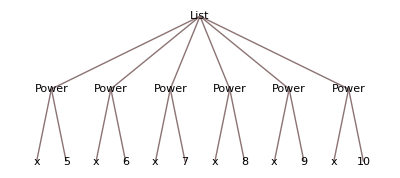

```mathematica
TreeForm@(x^Range[5,10])
```

```mathematica
x^Range[5,10]/.Power->Plus
```

{5+x,6+x,7+x,8+x,9+x,10+x}

```mathematica
5+x==x+5
```

True

```mathematica
{x,y}//.{x->y,y->x}
```

ReplaceRepeated::rrlim: Exiting after {x,y} scanned 65536 times.

{x,y}

```mathematica
FactorInteger[65536]
```

{{2,16}}

### Exercise Subsection

What does the following cell do when evaluated?

```mathematica
Clear[NoRepeats]
```

```mathematica
NoRepeats[L_List/;And[Length@L>0,Flatten@L==L]]:=L//.{x___,a_,y___,a_,z___}->{x,a,y,z}
```

```mathematica
NoRepeats[{1,2,3,4,5,4,2,1}]
```

{1,2,3,4,5}

### Exercise Subsection

The NSolve function produces a list of rules that solve the given equation, for example, consider the next cell.

```mathematica
solutions=NSolve[1320-3092 x+2338 x^2-571 x^3+17 x^4-28 x^5+21 x^6-5 x^7-60 x^21+140 x^22-105 x^23+25 x^24-12 x^55+28 x^56-21 x^57+5 x^58== 0, x]
```

{{x→-1.08967-0.0672631 ⅈ},{x→-1.08967+0.0672631 ⅈ},{x→-1.06919-0.182733 ⅈ},{x→-1.06919+0.182733 ⅈ},{x→-1.05052-0.307232 ⅈ},{x→-1.05052+0.307232 ⅈ},{x→-0.999016-0.427734 ⅈ},{x→-0.999016+0.427734 ⅈ},{x→-0.950112-0.530761 ⅈ},{x→-0.950112+0.530761 ⅈ},{x→-0.882774-0.6454 ⅈ},{x→-0.882774+0.6454 ⅈ},{x→-0.797737-0.73332 ⅈ},{x→-0.797737+0.73332 ⅈ},{x→-0.718481-0.823261 ⅈ},{x→-0.718481+0.823261 ⅈ},{x→-0.610472-0.902379 ⅈ},{x→-0.610472+0.902379 ⅈ},{x→-0.510175-0.958089 ⅈ},{x→-0.510175+0.958089 ⅈ},{x→-0.396897-1.02005 ⅈ},{x→-0.396897+1.02005 ⅈ},{x→-0.272459-1.05044 ⅈ},{x→-0.272459+1.05044 ⅈ},{x→-0.160359-1.07853 ⅈ},{x→-0.160359+1.07853 ⅈ},{x→-0.0267638-1.09228 ⅈ},{x→-0.0267638+1.09228 ⅈ},{x→0.0918091-1.08016 ⅈ},{x→0.0918091+1.08016 ⅈ},{x→0.215108-1.0726 ⅈ},{x→0.215108+1.0726 ⅈ},{x→0.341553-1.03276 ⅈ},{x→0.341553+1.03276 ⅈ},{x→0.447312-0.990583 ⅈ},{x→0.447312+0.990583 ⅈ},{x→0.566884-0.935562 ⅈ},{x→0.566884+0.935562 ⅈ},{x→0.663501-0.856745 ⅈ},{x→0.663501+0.856745 ⅈ},{x→0.757412-0.785904 ⅈ},{x→0.757412+0.785904 ⅈ},{x→0.847429-0.686165 ⅈ},{x→0.847429+0.686165 ⅈ},{x→0.910382-0.58886 ⅈ},{x→0.910382+0.58886 ⅈ},{x→0.981485-0.48369 ⅈ},{x→0.981485+0.48369 ⅈ},{x→1.},{x→1.02406-0.360859 ⅈ},{x→1.02406+0.360859 ⅈ},{x→1.05934-0.252088 ⅈ},{x→1.05934+0.252088 ⅈ},{x→1.08372},{x→1.08649-0.121227 ⅈ},{x→1.08649+0.121227 ⅈ},{x→1.2},{x→2.}}

Use a pattern and to change the variable solutions to a list of complex numbers instead of a list of rules.  Then, use a pattern and use Cases to select those values that are real.

```mathematica
Cases[solutions/.{x->a_}->a,a_/;Element[a,Reals]]
```

{1.,1.08372,1.2,2.}

## Iteration

### Exercise Subsection

Achieve the same output as the following cell in a couple of different ways, one of which should involve Table.

```mathematica
Do[Print[i],{i,Prime@Range@5}]
```

2

3

5

7

11

```mathematica
Table[i,{i,Prime@Range@5}]
```

{2,3,5,7,11}

```mathematica
Prime@Range@5
```

{2,3,5,7,11}

### Exercise Subsection

Use While to find the first prime number larger than 11 that has only the digit 1.

```mathematica
n=111;
While[Not@PrimeQ@n,n=10n+1]//Timing
n
```

{0.000075,Null}

1111111111111111111

### Exercise Subsection

Use While to find the smallest positive integer n such that 529^3 + 132^3 n is divisible by 262417.

### Exercise Subsection

Find the first prime number that contains at least one of each of the digits 0 through 9.

```mathematica
DigitCount[3113414231]
```

{4,1,3,2,0,0,0,0,0,0}

This is a tricky problem since brute force will not work.

```mathematica
n=NextPrime[10^9];
While[MemberQ[DigitCount@n,0],n=NextPrime@n]
```

$Aborted

```mathematica
n
```

1023267673

Next we try all integers with 10 distinct digits each used once (making it quicker, we select those without a leading 0 and without last digit other than 1,3,7,9).

```mathematica
SelectFirst[FromDigits/@Select[Permutations[Range@10-1],First@#!=0&&Not[MemberQ[{0,2,4,5,6,8},Last@#]]&],PrimeQ]
```

Missing[NotFound]

Next we move up to all integers that start with a 1, use a 0 two times, and then use 2,...,9 each once.

```mathematica
SelectFirst[FromDigits/@(Join[{1},#]&/@Select[Permutations[{0,0,2,3,4,5,6,7,8,9}],Not[MemberQ[{0,2,4,5,6,8},Last@#]]&]),PrimeQ]
```

Missing[NotFound]

Next we move up to all integers that start with a 1, use a 1 two times, and then use 2, ..., 9 each once .

```mathematica
SelectFirst[FromDigits/@(Join[{1},#]&/@Select[Permutations[Range@10-1],Not[MemberQ[{0,2,4,5,6,8},Last@#]]&]),PrimeQ]
```

10123457689

### Exercise Subsection

Find all positive integer pairs {a,b} such that a,b <=10 and a^2 + b^2 is a perfect square.

```mathematica
Cases[Tuples[Range@1000,2],{a_,b_}/;IntegerQ[Sqrt[a^2+b^2]]]//Timing
```

```mathematica
L={};
For[a=1,a<=1000,a=a+1,For[b=1,b<=1000,b+=1,If[IntegerQ[Sqrt[a^2+b^2]],L=Join[L,{{a,b}}]]]]//Timing
L
```

{3.669,Null}

{{3,4},{4,3},{5,12},{6,8},{7,24},{8,6},{8,15},{9,12},{9,40},{10,24},{11,60},{12,5},{12,9},{12,16},{12,35},{13,84},{14,48},{15,8},{15,20},{15,36},{15,112},{16,12},{16,30},{16,63},{17,144},{18,24},{18,80},{19,180},{20,15},{20,21},{20,48},{20,99},{21,20},{21,28},{21,72},{21,220},{22,120},{23,264},{24,7},{24,10},{24,18},{24,32},{24,45},{24,70},{24,143},{25,60},{25,312},{26,168},{27,36},{27,120},{27,364},{28,21},{28,45},{28,96},{28,195},{29,420},{30,16},{30,40},{30,72},{30,224},{31,480},{32,24},{32,60},{32,126},{32,255},{33,44},{33,56},{33,180},{33,544},{34,288},{35,12},{35,84},{35,120},{35,612},{36,15},{36,27},{36,48},{36,77},{36,105},{36,160},{36,323},{37,684},{38,360},{39,52},{39,80},{39,252},{39,760},{40,9},{40,30},{40,42},{40,75},{40,96},{40,198},{40,399},{41,840},{42,40},{42,56},{42,144},{42,440},{43,924},{44,33},{44,117},{44,240},{44,483},{45,24},{45,28},{45,60},{45,108},{45,200},{45,336},{46,528},{48,14},{48,20},{48,36},{48,55},{48,64},{48,90},{48,140},{48,189},{48,286},{48,575},{49,168},{50,120},{50,624},{51,68},{51,140},{51,432},{52,39},{52,165},{52,336},{52,675},{54,72},{54,240},{54,728},{55,48},{55,132},{55,300},{56,33},{56,42},{56,90},{56,105},{56,192},{56,390},{56,783},{57,76},{57,176},{57,540},{58,840},{60,11},{60,25},{60,32},{60,45},{60,63},{60,80},{60,91},{60,144},{60,175},{60,221},{60,297},{60,448},{60,899},{62,960},{63,16},{63,60},{63,84},{63,216},{63,280},{63,660},{64,48},{64,120},{64,252},{64,510},{65,72},{65,156},{65,420},{66,88},{66,112},{66,360},{68,51},{68,285},{68,576},{69,92},{69,260},{69,792},{70,24},{70,168},{70,240},{72,21},{72,30},{72,54},{72,65},{72,96},{72,135},{72,154},{72,210},{72,320},{72,429},{72,646},{75,40},{75,100},{75,180},{75,308},{75,560},{75,936},{76,57},{76,357},{76,720},{77,36},{77,264},{77,420},{78,104},{78,160},{78,504},{80,18},{80,39},{80,60},{80,84},{80,150},{80,192},{80,315},{80,396},{80,798},{81,108},{81,360},{84,13},{84,35},{84,63},{84,80},{84,112},{84,135},{84,187},{84,245},{84,288},{84,437},{84,585},{84,880},{85,132},{85,204},{85,720},{87,116},{87,416},{88,66},{88,105},{88,165},{88,234},{88,480},{88,966},{90,48},{90,56},{90,120},{90,216},{90,400},{90,672},{91,60},{91,312},{91,588},{92,69},{92,525},{93,124},{93,476},{95,168},{95,228},{95,900},{96,28},{96,40},{96,72},{96,110},{96,128},{96,180},{96,247},{96,280},{96,378},{96,572},{96,765},{98,336},{99,20},{99,132},{99,168},{99,440},{99,540},{100,75},{100,105},{100,240},{100,495},{100,621},{102,136},{102,280},{102,864},{104,78},{104,153},{104,195},{104,330},{104,672},{105,36},{105,56},{105,88},{105,100},{105,140},{105,208},{105,252},{105,360},{105,608},{105,784},{108,45},{108,81},{108,144},{108,231},{108,315},{108,480},{108,725},{108,969},{110,96},{110,264},{110,600},{111,148},{111,680},{112,15},{112,66},{112,84},{112,180},{112,210},{112,384},{112,441},{112,780},{114,152},{114,352},{115,252},{115,276},{116,87},{116,837},{117,44},{117,156},{117,240},{117,520},{117,756},{119,120},{119,408},{120,22},{120,27},{120,35},{120,50},{120,64},{120,90},{120,119},{120,126},{120,160},{120,182},{120,209},{120,225},{120,288},{120,350},{120,391},{120,442},{120,594},{120,715},{120,896},{121,660},{123,164},{123,836},{124,93},{124,957},{125,300},{126,32},{126,120},{126,168},{126,432},{126,560},{128,96},{128,240},{128,504},{129,172},{129,920},{130,144},{130,312},{130,840},{132,55},{132,85},{132,99},{132,176},{132,224},{132,351},{132,385},{132,475},{132,720},{133,156},{133,456},{135,72},{135,84},{135,180},{135,324},{135,352},{135,600},{136,102},{136,255},{136,273},{136,570},{138,184},{138,520},{140,48},{140,51},{140,105},{140,147},{140,171},{140,225},{140,336},{140,480},{140,693},{140,975},{141,188},{143,24},{143,780},{143,924},{144,17},{144,42},{144,60},{144,108},{144,130},{144,165},{144,192},{144,270},{144,308},{144,420},{144,567},{144,640},{144,858},{145,348},{145,408},{147,140},{147,196},{147,504},{148,111},{150,80},{150,200},{150,360},{150,616},{152,114},{152,285},{152,345},{152,714},{153,104},{153,204},{153,420},{153,680},{154,72},{154,528},{154,840},{155,372},{155,468},{156,65},{156,117},{156,133},{156,208},{156,320},{156,455},{156,495},{156,667},{159,212},{160,36},{160,78},{160,120},{160,168},{160,231},{160,300},{160,384},{160,630},{160,792},{161,240},{161,552},{162,216},{162,720},{164,123},{165,52},{165,88},{165,144},{165,220},{165,280},{165,396},{165,532},{165,900},{168,26},{168,49},{168,70},{168,95},{168,99},{168,126},{168,160},{168,224},{168,270},{168,315},{168,374},{168,425},{168,490},{168,576},{168,775},{168,874},{170,264},{170,408},{171,140},{171,228},{171,528},{171,760},{172,129},{174,232},{174,832},{175,60},{175,288},{175,420},{175,600},{176,57},{176,132},{176,210},{176,330},{176,468},{176,693},{176,960},{177,236},{180,19},{180,33},{180,75},{180,96},{180,112},{180,135},{180,189},{180,240},{180,273},{180,299},{180,385},{180,432},{180,525},{180,663},{180,800},{180,891},{182,120},{182,624},{183,244},{184,138},{184,345},{184,513},{185,444},{185,672},{186,248},{186,952},{187,84},{188,141},{189,48},{189,180},{189,252},{189,340},{189,648},{189,840},{190,336},{190,456},{192,56},{192,80},{192,144},{192,220},{192,256},{192,360},{192,494},{192,560},{192,756},{195,28},{195,104},{195,216},{195,260},{195,400},{195,468},{195,748},{196,147},{196,315},{196,672},{198,40},{198,264},{198,336},{198,880},{200,45},{200,150},{200,210},{200,375},{200,480},{200,609},{200,990},{201,268},{203,396},{203,696},{204,85},{204,153},{204,253},{204,272},{204,560},{204,595},{204,855},{205,492},{205,828},{207,224},{207,276},{207,780},{207,920},{208,105},{208,156},{208,306},{208,390},{208,660},{208,819},{209,120},{210,72},{210,112},{210,176},{210,200},{210,280},{210,416},{210,504},{210,720},{212,159},{213,284},{215,516},{215,912},{216,63},{216,90},{216,162},{216,195},{216,288},{216,405},{216,462},{216,630},{216,713},{216,960},{217,456},{217,744},{219,292},{220,21},{220,165},{220,192},{220,231},{220,459},{220,528},{220,585},{221,60},{222,296},{224,30},{224,132},{224,168},{224,207},{224,360},{224,420},{224,768},{224,882},{225,120},{225,140},{225,272},{225,300},{225,540},{225,924},{225,1000},{228,95},{228,171},{228,304},{228,325},{228,665},{228,704},{230,504},{230,552},{231,108},{231,160},{231,220},{231,308},{231,392},{231,520},{231,792},{232,174},{232,435},{232,825},{234,88},{234,312},{234,480},{235,564},{236,177},{237,316},{238,240},{238,816},{240,44},{240,54},{240,70},{240,100},{240,117},{240,128},{240,161},{240,180},{240,238},{240,252},{240,275},{240,320},{240,364},{240,418},{240,450},{240,551},{240,576},{240,700},{240,782},{240,884},{240,945},{243,324},{244,183},{245,84},{245,588},{245,840},{246,328},{247,96},{248,186},{248,465},{248,945},{249,332},{250,600},{252,39},{252,64},{252,105},{252,115},{252,189},{252,240},{252,275},{252,336},{252,405},{252,539},{252,561},{252,735},{252,864},{253,204},{255,32},{255,136},{255,340},{255,396},{255,612},{255,700},{256,192},{256,480},{258,344},{259,660},{259,888},{260,69},{260,195},{260,273},{260,288},{260,624},{260,651},{260,825},{261,348},{261,380},{264,23},{264,77},{264,110},{264,170},{264,198},{264,315},{264,352},{264,448},{264,495},{264,702},{264,770},{264,950},{265,636},{266,312},{266,912},{267,356},{268,201},{270,144},{270,168},{270,360},{270,648},{270,704},{272,204},{272,225},{272,510},{272,546},{273,136},{273,180},{273,260},{273,364},{273,560},{273,736},{273,936},{275,240},{275,252},{275,660},{276,115},{276,207},{276,368},{276,493},{276,805},{279,372},{279,440},{280,63},{280,96},{280,102},{280,165},{280,210},{280,294},{280,342},{280,351},{280,450},{280,525},{280,672},{280,759},{280,960},{282,376},{284,213},{285,68},{285,152},{285,380},{285,504},{285,684},{285,880},{286,48},{287,816},{287,984},{288,34},{288,84},{288,120},{288,175},{288,216},{288,260},{288,330},{288,384},{288,540},{288,616},{288,741},{288,840},{290,696},{290,816},{291,388},{292,219},{294,280},{294,392},{295,708},{296,222},{296,555},{297,60},{297,304},{297,396},{297,504},{299,180},{300,55},{300,125},{300,160},{300,225},{300,315},{300,400},{300,455},{300,589},{300,720},{300,875},{301,900},{303,404},{304,228},{304,297},{304,570},{304,690},{305,732},{306,208},{306,408},{306,840},{308,75},{308,144},{308,231},{308,435},{308,495},{308,819},{309,412},{310,744},{310,936},{312,25},{312,91},{312,130},{312,234},{312,266},{312,416},{312,459},{312,585},{312,640},{312,910},{312,990},{315,80},{315,108},{315,168},{315,196},{315,264},{315,300},{315,420},{315,572},{315,624},{315,756},{315,988},{316,237},{318,424},{319,360},{320,72},{320,156},{320,240},{320,336},{320,462},{320,600},{320,768},{320,999},{321,428},{322,480},{323,36},{324,135},{324,243},{324,432},{324,693},{324,945},{325,228},{325,360},{325,780},{327,436},{328,246},{328,615},{330,104},{330,176},{330,288},{330,440},{330,560},{330,792},{332,249},{333,444},{333,644},{335,804},{336,45},{336,52},{336,98},{336,140},{336,190},{336,198},{336,252},{336,320},{336,377},{336,385},{336,448},{336,527},{336,540},{336,630},{336,748},{336,850},{336,980},{339,452},{340,189},{340,255},{340,357},{340,528},{340,816},{341,420},{342,280},{342,456},{344,258},{344,645},{345,152},{345,184},{345,460},{345,756},{345,828},{348,145},{348,261},{348,464},{348,805},{350,120},{350,576},{350,840},{351,132},{351,280},{351,468},{351,720},{352,114},{352,135},{352,264},{352,420},{352,660},{352,936},{354,472},{355,852},{356,267},{357,76},{357,340},{357,360},{357,476},{357,980},{360,38},{360,66},{360,81},{360,105},{360,150},{360,192},{360,224},{360,270},{360,319},{360,325},{360,357},{360,378},{360,480},{360,546},{360,598},{360,627},{360,675},{360,770},{360,864},{363,484},{363,616},{364,27},{364,240},{364,273},{364,585},{364,627},{365,876},{366,488},{368,276},{368,465},{368,690},{369,492},{369,800},{370,888},{372,155},{372,279},{372,496},{372,925},{374,168},{375,200},{375,500},{375,900},{376,282},{376,705},{377,336},{378,96},{378,360},{378,504},{378,680},{380,261},{380,285},{380,399},{380,672},{380,912},{381,508},{384,112},{384,160},{384,288},{384,440},{384,512},{384,720},{384,988},{385,132},{385,180},{385,336},{385,552},{385,924},{387,516},{387,884},{388,291},{390,56},{390,208},{390,432},{390,520},{390,800},{390,936},{391,120},{392,231},{392,294},{392,630},{392,735},{393,524},{395,948},{396,80},{396,165},{396,203},{396,255},{396,297},{396,403},{396,528},{396,672},{396,847},{399,40},{399,380},{399,468},{399,532},{400,90},{400,195},{400,300},{400,420},{400,561},{400,750},{400,960},{402,536},{403,396},{404,303},{405,216},{405,252},{405,540},{405,972},{406,792},{407,624},{408,119},{408,145},{408,170},{408,306},{408,506},{408,544},{408,765},{408,819},{410,984},{411,548},{412,309},{414,448},{414,552},{415,996},{416,87},{416,210},{416,312},{416,612},{416,780},{417,556},{418,240},{420,29},{420,65},{420,77},{420,144},{420,153},{420,175},{420,224},{420,315},{420,341},{420,352},{420,400},{420,441},{420,513},{420,560},{420,637},{420,675},{420,832},{420,851},{420,935},{423,564},{424,318},{424,795},{425,168},{425,660},{426,568},{428,321},{429,72},{429,460},{429,572},{429,700},{429,728},{429,880},{432,51},{432,126},{432,180},{432,324},{432,390},{432,495},{432,576},{432,665},{432,810},{432,924},{434,912},{435,232},{435,308},{435,580},{436,327},{437,84},{438,584},{440,42},{440,99},{440,279},{440,330},{440,384},{440,462},{440,525},{440,825},{440,918},{441,112},{441,420},{441,588},{442,120},{444,185},{444,333},{444,592},{447,596},{448,60},{448,264},{448,336},{448,414},{448,720},{448,840},{448,975},{450,240},{450,280},{450,544},{450,600},{451,780},{452,339},{453,604},{455,156},{455,300},{455,504},{455,528},{456,133},{456,190},{456,217},{456,342},{456,608},{456,650},{456,855},{459,220},{459,312},{459,612},{460,345},{460,429},{460,483},{462,216},{462,320},{462,440},{462,616},{462,784},{464,348},{464,777},{464,870},{465,248},{465,368},{465,620},{468,155},{468,176},{468,195},{468,351},{468,399},{468,595},{468,624},{468,960},{471,628},{472,354},{472,885},{473,864},{474,632},{475,132},{475,840},{476,93},{476,357},{476,480},{476,765},{477,636},{480,31},{480,88},{480,108},{480,140},{480,200},{480,234},{480,256},{480,322},{480,360},{480,476},{480,504},{480,550},{480,640},{480,693},{480,728},{480,836},{480,900},{481,600},{483,44},{483,460},{483,644},{483,720},{484,363},{486,648},{488,366},{488,915},{489,652},{490,168},{492,205},{492,369},{492,656},{493,276},{494,192},{495,100},{495,156},{495,264},{495,308},{495,432},{495,660},{495,840},{495,952},{496,372},{496,897},{496,930},{498,664},{500,375},{500,525},{501,668},{504,78},{504,128},{504,147},{504,210},{504,230},{504,285},{504,297},{504,378},{504,455},{504,480},{504,550},{504,672},{504,703},{504,810},{504,945},{506,408},{507,676},{508,381},{510,64},{510,272},{510,680},{510,792},{512,384},{512,960},{513,184},{513,420},{513,684},{516,215},{516,387},{516,688},{519,692},{520,117},{520,138},{520,231},{520,390},{520,546},{520,576},{520,765},{520,975},{522,696},{522,760},{524,393},{525,92},{525,180},{525,280},{525,440},{525,500},{525,700},{525,864},{527,336},{528,46},{528,154},{528,171},{528,220},{528,340},{528,396},{528,455},{528,605},{528,630},{528,704},{528,896},{528,990},{531,708},{532,165},{532,399},{532,624},{532,855},{533,756},{534,712},{536,402},{537,716},{539,252},{540,57},{540,99},{540,225},{540,288},{540,336},{540,405},{540,567},{540,629},{540,720},{540,819},{540,897},{543,724},{544,33},{544,408},{544,450},{546,272},{546,360},{546,520},{546,728},{548,411},{549,732},{550,480},{550,504},{551,240},{552,161},{552,230},{552,385},{552,414},{552,736},{552,986},{555,296},{555,572},{555,740},{556,417},{558,744},{558,880},{559,840},{560,75},{560,126},{560,192},{560,204},{560,273},{560,330},{560,420},{560,588},{560,684},{560,702},{560,900},{561,252},{561,400},{561,748},{561,952},{564,235},{564,423},{564,752},{567,144},{567,540},{567,756},{568,426},{570,136},{570,304},{570,760},{572,96},{572,315},{572,429},{572,555},{573,764},{575,48},{576,68},{576,168},{576,240},{576,350},{576,432},{576,520},{576,660},{576,768},{576,943},{579,772},{580,435},{580,609},{580,741},{582,776},{584,438},{585,84},{585,220},{585,312},{585,364},{585,648},{585,780},{585,928},{588,91},{588,245},{588,441},{588,560},{588,784},{588,945},{589,300},{591,788},{592,444},{594,120},{594,608},{594,792},{595,204},{595,468},{595,600},{595,924},{596,447},{597,796},{598,360},{600,110},{600,135},{600,175},{600,250},{600,320},{600,450},{600,481},{600,595},{600,630},{600,800},{600,910},{603,804},{604,453},{605,528},{606,808},{608,105},{608,456},{608,594},{609,200},{609,580},{609,812},{612,35},{612,255},{612,416},{612,459},{612,759},{612,816},{615,328},{615,728},{615,820},{616,150},{616,288},{616,363},{616,462},{616,663},{616,735},{616,870},{616,990},{618,824},{620,465},{620,651},{620,861},{621,100},{621,672},{621,828},{624,50},{624,182},{624,260},{624,315},{624,407},{624,468},{624,532},{624,715},{624,832},{624,918},{627,360},{627,364},{627,836},{628,471},{629,540},{630,160},{630,216},{630,336},{630,392},{630,528},{630,600},{630,840},{632,474},{633,844},{636,265},{636,477},{636,848},{637,420},{638,720},{639,852},{640,144},{640,312},{640,480},{640,672},{640,924},{642,856},{644,333},{644,483},{644,960},{645,344},{645,812},{645,860},{646,72},{648,189},{648,270},{648,486},{648,585},{648,864},{650,456},{650,720},{651,260},{651,620},{651,868},{652,489},{654,872},{656,492},{657,876},{660,63},{660,121},{660,208},{660,259},{660,275},{660,352},{660,425},{660,495},{660,576},{660,693},{660,779},{660,880},{660,989},{663,180},{663,616},{663,884},{664,498},{665,228},{665,432},{665,780},{666,888},{667,156},{668,501},{669,892},{672,90},{672,104},{672,185},{672,196},{672,280},{672,380},{672,396},{672,504},{672,621},{672,640},{672,754},{672,770},{672,896},{675,52},{675,360},{675,420},{675,816},{675,900},{676,507},{678,904},{680,111},{680,153},{680,378},{680,510},{680,714},{681,908},{682,840},{684,37},{684,285},{684,513},{684,560},{684,912},{684,975},{687,916},{688,516},{690,304},{690,368},{690,920},{692,519},{693,140},{693,176},{693,324},{693,480},{693,660},{693,924},{696,203},{696,290},{696,522},{696,697},{696,928},{697,696},{699,932},{700,240},{700,255},{700,429},{700,525},{700,735},{700,855},{702,264},{702,560},{702,936},{703,504},{704,228},{704,270},{704,528},{704,840},{704,903},{705,376},{705,940},{705,992},{708,295},{708,531},{708,944},{711,948},{712,534},{713,216},{714,152},{714,680},{714,720},{714,952},{715,120},{715,624},{715,792},{716,537},{717,956},{720,76},{720,85},{720,132},{720,162},{720,210},{720,300},{720,351},{720,384},{720,448},{720,483},{720,540},{720,638},{720,650},{720,714},{720,756},{720,825},{720,960},{723,964},{724,543},{725,108},{726,968},{728,54},{728,429},{728,480},{728,546},{728,615},{729,972},{731,780},{732,305},{732,549},{732,976},{735,252},{735,392},{735,616},{735,700},{735,980},{736,273},{736,552},{736,930},{738,984},{740,555},{740,777},{741,288},{741,580},{741,988},{744,217},{744,310},{744,558},{744,817},{744,992},{747,996},{748,195},{748,336},{748,561},{750,400},{750,1000},{752,564},{754,672},{756,117},{756,192},{756,315},{756,345},{756,533},{756,567},{756,720},{756,825},{759,280},{759,612},{760,39},{760,171},{760,522},{760,570},{760,798},{764,573},{765,96},{765,408},{765,476},{765,520},{765,868},{768,224},{768,320},{768,576},{768,880},{770,264},{770,360},{770,672},{772,579},{775,168},{776,582},{777,464},{777,740},{779,660},{780,112},{780,143},{780,207},{780,325},{780,416},{780,451},{780,585},{780,665},{780,731},{780,819},{780,864},{782,240},{783,56},{784,105},{784,462},{784,588},{788,591},{792,69},{792,160},{792,231},{792,330},{792,406},{792,510},{792,594},{792,715},{792,806},{792,945},{795,424},{796,597},{798,80},{798,760},{798,936},{799,960},{800,180},{800,369},{800,390},{800,600},{800,840},{804,335},{804,603},{805,276},{805,348},{806,792},{808,606},{810,432},{810,504},{812,609},{812,645},{816,238},{816,287},{816,290},{816,340},{816,612},{816,675},{816,935},{817,744},{819,208},{819,308},{819,408},{819,540},{819,780},{820,615},{820,861},{824,618},{825,232},{825,260},{825,440},{825,720},{825,756},{828,205},{828,345},{828,621},{828,896},{832,174},{832,420},{832,624},{832,855},{833,840},{836,123},{836,480},{836,627},{837,116},{840,41},{840,58},{840,130},{840,154},{840,189},{840,245},{840,288},{840,306},{840,350},{840,448},{840,475},{840,495},{840,559},{840,630},{840,682},{840,704},{840,800},{840,833},{840,882},{844,633},{845,936},{847,396},{848,636},{850,336},{851,420},{852,355},{852,639},{855,204},{855,456},{855,532},{855,700},{855,832},{856,642},{858,144},{858,920},{860,645},{860,903},{861,620},{861,820},{864,102},{864,252},{864,360},{864,473},{864,525},{864,648},{864,780},{864,990},{868,651},{868,765},{870,464},{870,616},{872,654},{874,168},{875,300},{876,365},{876,657},{880,84},{880,198},{880,285},{880,429},{880,558},{880,660},{880,768},{880,924},{882,224},{882,840},{884,240},{884,387},{884,663},{884,987},{885,472},{888,259},{888,370},{888,666},{891,180},{891,912},{892,669},{893,924},{896,120},{896,528},{896,672},{896,828},{897,496},{897,540},{899,60},{900,95},{900,165},{900,301},{900,375},{900,480},{900,560},{900,675},{900,945},{903,704},{903,860},{904,678},{908,681},{910,312},{910,600},{912,215},{912,266},{912,380},{912,434},{912,684},{912,891},{915,488},{916,687},{918,440},{918,624},{920,129},{920,207},{920,690},{920,858},{920,966},{924,43},{924,143},{924,225},{924,385},{924,432},{924,595},{924,640},{924,693},{924,880},{924,893},{925,372},{928,585},{928,696},{930,496},{930,736},{932,699},{935,420},{935,816},{936,75},{936,273},{936,310},{936,352},{936,390},{936,702},{936,798},{936,845},{940,705},{940,987},{943,576},{944,708},{945,240},{945,248},{945,324},{945,504},{945,588},{945,792},{945,900},{948,395},{948,711},{950,264},{952,186},{952,495},{952,561},{952,714},{952,960},{956,717},{957,124},{960,62},{960,176},{960,216},{960,280},{960,400},{960,468},{960,512},{960,644},{960,720},{960,799},{960,952},{964,723},{966,88},{966,920},{968,726},{969,108},{972,405},{972,729},{975,140},{975,448},{975,520},{975,684},{976,732},{980,336},{980,357},{980,735},{984,287},{984,410},{984,738},{986,552},{987,884},{987,940},{988,315},{988,384},{988,741},{989,660},{990,200},{990,312},{990,528},{990,616},{990,864},{992,705},{992,744},{996,415},{996,747},{999,320},{1000,225},{1000,750}}

```mathematica
L
```

{{3,4},{4,3},{6,8},{8,6}}

### Exercise Subsection

Find a pair {q,r} of positive integers such that 17^2 + q^2 = r^2.

```mathematica
Cases[Tuples[Range@1000,2],{q_,r_}/;17^2+q^2==r^2]
```

{{144,145}}

## Nest

### Exercise Subsection

Let f[x_]:=1/(1+x).  Use Nest to find the value of f[f[f[...1]]]]] where the iteration is applied 100 times to the number 1.  What is the numerical difference between this and iterating f one million times to 1?

```mathematica
f[x_]:=1/(1+x)
```

```mathematica
Nest[f,1,100]//N
Nest[f,1,10^6]//N
```

0.618034

0.618034

### Exercise Subsection

Find the difference between the numerical values of 2/Pi and the product of the form 

(Sqrt[2]/2)(Sqrt[2+Sqrt[2]]/2)(Sqrt[2+Sqrt[2+Sqrt[2]]]/2)...

where there are 25 terms here.

```mathematica
Times@@(NestList[Sqrt[#+2]/2&,0,25][[2;;]])//N
```

0.0114219

### Exercise Subsection

What does the following cell do?

```mathematica
NestWhile[#-2&,2^100-1,CompositeQ]//Timing
```

{0.000411,1267650600228229401496703205361}

```mathematica
NestWhile[#-1&,2^100-1,CompositeQ]//Timing
```

{0.000488,1267650600228229401496703205361}

This command iteratively subtracts 2 from the integer 2^100-1 until we find a prime number.

### Exercise Subsection

Use NestWhile to find the first prime number larger than 11 that has only the digit 1.

```mathematica
NestWhile[10#+1&,111,CompositeQ]
```

1111111111111111111